```mathematica
(*  DEMAND FOR GOOD Y       *)
```

```mathematica
y[p_, x0_, y0_, pi_, a_]:= ((x0 + p y0)*(1 - pi)^(1/a))/((p * pi)^(1/a) +p(1 - pi)^(1/a))
```

```mathematica
y[4, 2, 18, 0.4167, 2]
```

13.0043

```mathematica
yB[p_]:= (24 + 2 p) 7^0.5/((5 p)^0.5 + p 7^0.5)
```

```mathematica
yB[4]
```

5.6236

```mathematica
yS[p_]:= (2 + 18 p) 7^0.5/((5 p)^0.5 + p 7^0.5)
```

```mathematica
yS[4]
```

13.0046

```mathematica
(*  AN EQUIVALENT EXPRESSION FOR DEMAND     *)
```

```mathematica
A[p_, pi_, a_]:= (p * pi/(1 - pi))^(1/a)
```

```mathematica
Y[p_, x0_, y0_, pi_, a_]:= (x0 + p y0)/(A[p, pi, a] +p)
```

```mathematica
{Y[2.36, 2, 18, 5/12, 2], N[Y[4, 24, 2, 5/12, 2]]}
```

{12.1585,5.6236}

```mathematica
(*  EXCESS DEMAND IS THE CHANGE BETWEEN THE FINAL DEMAND FOR Y AND   *)
(*  THE AGENT'S ENDOWMENT OF Y.                                      *)
```

```mathematica
Z[p_, x0_, y0_, pi_, a_]:= Y[p, x0, y0, pi, a] - y0
```

```mathematica
{Z[2.366, 2, 18, 5/12, 2], Z[2.366, 24, 2, 5/12, 2]}
```

{-5.83742,5.83742}

```mathematica
Z[p_]:= Z[p, 2, 18, 5/12, 2] + Z[p, 24, 2, 5/12, 2]
```

```mathematica
N[Z[4]]
```

-1.37184

```mathematica
(*  The next several steps modify the ticks and tick labels on the   *)
(*  excess demand graph to move them above the horizontal axis.      *)
(*  I did this so that the dotted lines for the excess demand        *)
(*  would not run through the axis label at p = 4.                   *)
```

```mathematica
plt = Plot[Z[p], {p, 0.01, 6}, PlotRange -> {{0, 5}, {-2, 6}}, AxesLabel-> {"p", "Z(p)"},LabelStyle->{FontSize->11,Black}];
```

```mathematica
tks=AbsoluteOptions[plt,Ticks];
```

```mathematica
xTks=Map[If[Head[#[[2]]]===Real,ReplacePart[#,{"",{.01,0}},{{2},{3}},{{1},{2}}],#]&,tks[[1,2,1]]];
```

```mathematica
tklbls = Table[Style[Text[i, {i, 0.35}], FontSize->11],{i,1,5}];
```

```mathematica
(*  This graph shows the excess demand function and it emphasizes    *)
(*  the magnitude of excess demand at p = 4 with dotted lines.       *)
```

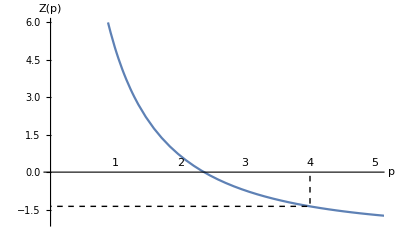

```mathematica
Show[Plot[Z[p], {p, 0.01, 6}, Ticks -> {xTks,Automatic},Epilog -> tklbls,PlotRange -> {{0, 5.04}, {-2, 6}}, AxesLabel-> {"p", "Z(p)"},LabelStyle->{FontSize->11,Black}], Graphics[{Dashing[{0.01, 0.01, 0.01}], Line[{{4, -0.15}, {4, -1.37222}, {0, -1.37222}}]}]]
```

```mathematica
(*  If the market excess demand is set equal to zero the equilibrium    *)
(*  price can be determined with a little bit of algebra.  It is        *)
(*  p* = 1.3^2 * 1.4.                                                  *)
```

```mathematica
1.3 * 1.3 * 1.4
```

2.366

```mathematica
Z[2.366]
```

-8.88178×10^-16

```mathematica
(*  We can use the adjustment equation (17) in the lecture notes to    *)
(*  model an iterative price adjustment process.                       *)
```

```mathematica
4 + 0.1 * Z[4]
```

3.86282

```mathematica
(*  Suppose that we define an adjustment process using the       *)
(*  excess demand function Z[p] by the equation                  *)
```

```mathematica
f[p_, a_]:= Join[p, {p[[-1]] + a  * Z[p[[-1]]]}]
```

```mathematica
(*  We can use f[p, a] to get a price path step-by-step.        *)
```

```mathematica
p1 = f[{4}, 0.1]
```

{4,3.86282}

```mathematica
p2 = f[p1, 0.1]
```

{4,3.86282,3.73209}

```mathematica
p3 = f[p2, 0.1]
```

{4,3.86282,3.73209,3.60805}

```mathematica
p4 = f[p3, 0.1]
```

{4,3.86282,3.73209,3.60805,3.4909}

```mathematica
p5 = f[p4, 0.1]
```

{4,3.86282,3.73209,3.60805,3.4909,3.38081}

```mathematica
(*  Problem 10   *)
(*  Write a function that will iteratively determine prices like the    *)
(*  prices above.  Use the output above to verify that your function    *)
(*  works properly.  Then use your function to evaluate the price       *)
(*  path starting at p0 = 4 with an adjustment rate f 0.02 with 175     *)
(*  iterations.
```

```mathematica
PriceSequence[p_, a_, n_]:= Module[{k, pNew, pTmp}, 
k = Length[p];
pTmp = p;
Label[start];
(*  Write some code here to make a function that generates prices  *)
(*  iteratively.  I was able to do this with 2 lines of code.      *)
k = k + 1;
If[k < n, Goto[start]];
Return[pTmp]]
```

```mathematica
PriceSequence[{4}, 0.1, 35]
```

{4,3.86278,3.73201,3.60794,3.49076,3.38064,3.27767,3.18191,3.09334,3.01188,2.93737,2.86961,2.80834,2.75323,2.70392,2.66003,2.62115,2.58687,2.55675,2.53041,2.50744,2.48748,2.47018,2.45522,2.44232,2.43122,2.42168,2.41349,2.40648,2.40047,2.39534,2.39095,2.3872,2.38401,2.38128}

```mathematica
PriceSequence[{4}, 0.02, 175]
```

```mathematica
(*  If we linearize the excess demand function at the equilbrium     *)
(*  we get a representation that is similar to an autoregressive     *)
(*  process.                                                         *)
```

```mathematica
Z'[2.366]
```

-1.49877

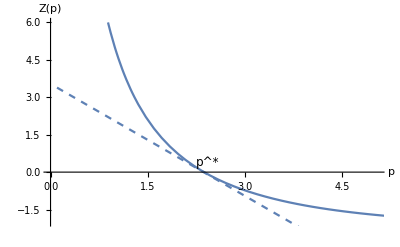

```mathematica
Show[Plot[Z[p], {p, 0.01, 6}, PlotRange -> {{0, 5.04}, {-2, 6}}, AxesLabel-> {"p", "Z(p)"},LabelStyle->{FontSize->11,Black}], 
Graphics[Text[StyleForm[Superscript["p", "*"],12],{2.42, 0.4}]], Plot[Z'[2.366] *(x - 2.36), {x, 0.1, 6}, PlotStyle -> Dashed]]
```